```mathematica
ClearAll["Global`*"]
```

## (*Simple Example To showcase How we can fit model through data points with constraint that the curve needs to pass through specific points.*)

## (*Style 1*)

```mathematica
data=Table[{i,i},{i,10}]
model=a+b x^2;
```

{{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10}}

```mathematica
(*UnRestructed Model*)
nlm=NonlinearModelFit[data,model,{a,b},x]//Normal
```

2.17582+0.0863422 x^2

```mathematica
(*Model restricted to pass through {5,5}:*)
nlmr=NonlinearModelFit[data,{model,(model/. x->5)==5},{a,b},x]//Normal
```

3.02359+0.0790566 x^2

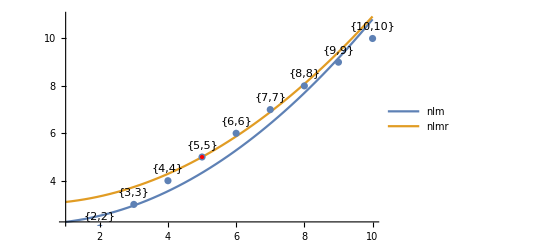

```mathematica
(*Picture*)
Show[Plot[{nlm,nlmr},{x,1,10},PlotStyle->Thick,PlotLegends->{"nlm","nlmr"}],ListPlot[Labeled[#,#,Top]&/@data],Graphics[{Red,PointSize[Large],Point[{5,5}]}]]
```

```mathematica
(*Style 2*)
```

```mathematica
model2[x_]:=a+b x^2;
nlm2=NonlinearModelFit[data,model2[x],{a,b},x]//Normal
nlmr2=NonlinearModelFit[data,{model2[x],model2[5]==5},{a,b},x]//Normal
```

2.17582+0.0863422 x^2

3.02359+0.0790566 x^2

0.875+0.125 x^2

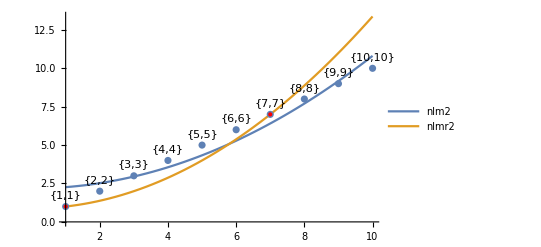

```mathematica
(*You can also have multiple constraints,e.g.,can force the fit to pass through two points {1,1} and {7,7}:*)
nlmr2=NonlinearModelFit[data,{model2[x],model2[1]==1&&model2[7]==7},{a,b},x]//Normal
Show[Plot[{nlm2,nlmr2},{x,1,10},PlotStyle->Thick,PlotLegends->{"nlm2","nlmr2"}],ListPlot[Labeled[#,#,Top]&/@data],Graphics[{Red,PointSize[Large],Point[{{1,1},{7,7}}]}]]
```

```mathematica
(*Trying out On Other Data*)
```

{{0,0.4},{π/64,0.425},{π/32,0.45},{(3 π)/64,0.475},{π/16,0.5},{(5 π)/64,0.525},{(3 π)/32,0.55},{(7 π)/64,0.575},{π/8,0.6},{(3 π)/20,0.59},{(7 π)/40,0.58},{π/5,0.57},{(9 π)/40,0.56},{π/4,0.55},{(11 π)/40,0.56},{(3 π)/10,0.57},{(13 π)/40,0.58},{(7 π)/20,0.59},{(3 π)/8,0.6},{(25 π)/64,0.575},{(13 π)/32,0.55},{(27 π)/64,0.525},{(7 π)/16,0.5},{(29 π)/64,0.475},{(15 π)/32,0.45},{(31 π)/64,0.425},{π/2,0.4}}

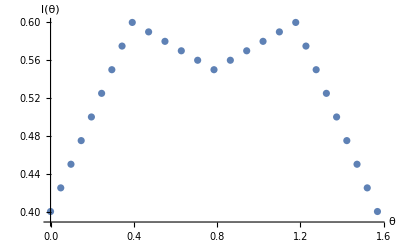

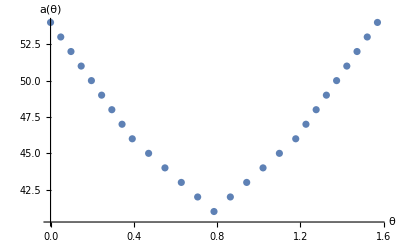

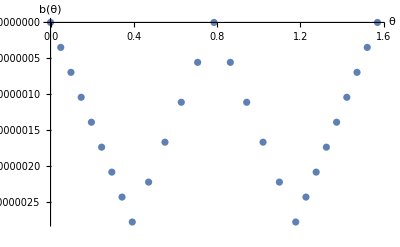

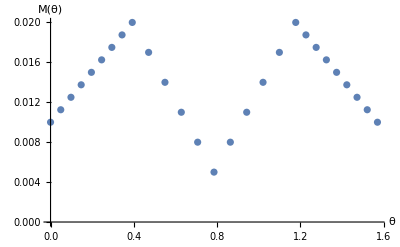

```mathematica
ldata=Union[Reverse[Table[{Pi/8-Pi/4*i/16,0.6-i*0.025},{i,1,8}]],Reverse[Table[{Pi/4-Pi/4*i/10,0.55+i*0.01},{i,0,5}]],Table[{Pi/4*(1+i/10),0.55+i*0.01},{i,1,5}],Table[{(3*Pi)/8+Pi/4*i/16,0.6-i*0.025},{i,1,8}]]
adata=Union[Reverse[Table[{Pi/8-Pi/4*i/16,46+i},{i,1,8}]],Reverse[Table[{Pi/4-Pi/4*i/10,41+i},{i,0,5}]],Table[{Pi/4*(1+i/10),41+i},{i,1,5}],Table[{(3*Pi)/8+Pi/4*i/16,46+i},{i,1,8}]];
bdata=Union[Reverse[Table[{Pi/8-Pi/4*i/16,-1/36*(1-i/8)*10^-4},{i,1,8}]],Reverse[Table[{Pi/4-Pi/4*i/10,-1/36*i/5*10^-4},{i,0,5}]],Table[{Pi/4*(1+i/10),-1/36*i/5*10^-4},{i,1,5}],Table[{(3*Pi)/8+Pi/4*i/16,-1/36*(1-i/8)*10^-4},{i,1,8}]];
Mdata=Union[Reverse[Table[{Pi/8-Pi/4*i/16,0.02-i*0.00125},{i,1,8}]],Reverse[Table[{Pi/4-Pi/4*i/10,0.005+i*0.003},{i,0,5}]],Table[{Pi/4*(1+i/10),0.005+i*0.003},{i,1,5}],Table[{(3*Pi)/8+Pi/4*i/16,0.02-i*0.00125},{i,1,8}]];
ListPlot[ldata,AxesLabel->{"θ","l(θ)"}]
ListPlot[adata,AxesLabel->{"θ","a(θ)"}]
ListPlot[bdata,AxesLabel->{"θ","b(θ)"}]
ListPlot[Mdata,AxesLabel->{"θ","M(θ)"}]
```

al+bl x^2+cl x^3+dl x^4+el x^5+fl x^6+gl x^7+hl x^8

0.4+3.78191 x^2-2.62561 x^3-27.7035 x^4+67.8046 x^5-64.4383 x^6+28.0069 x^7-4.63509 x^8

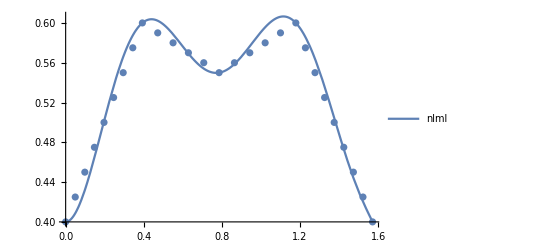

```mathematica
(*Fitting ldata*)
lmodel=al+bl x^2+cl x^3+dl x^4+el x^5+fl x^6+gl x^7+hl x^8
nlml=NonlinearModelFit[ldata,{lmodel,(lmodel/.x->0)==0.4,(lmodel/.x->Pi/8)==0.6,(lmodel/.x->Pi/4)==0.55,(lmodel/.x->(3*Pi)/8)==0.6,(lmodel/.x->Pi/2)==0.4},{al,bl,cl,dl,el,fl,gl,hl},x]//Normal
Show[Plot[nlml,{x,0,Pi/2},PlotStyle->Thick,PlotLegends->{"nlml"}],ListPlot[ldata]]
```

aa+ba x^2+ca x^3+da x^4

54.-80.0791 x^2+99.2733 x^3-30.7445 x^4

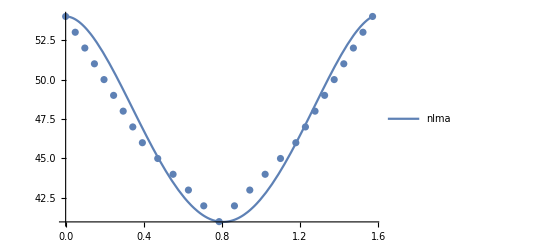

```mathematica
(*Fitting adata*)
amodel=aa+ba x^2+ca x^3+da x^4(*+ea x^5+fa x^6+ga x^7+ha x^8*)
(*nlma=NonlinearModelFit[adata,{amodel,(amodel/.x->0)==54,(amodel/.x->Pi/8)==46,(amodel/.x->Pi/4)==41,(amodel/.x->(3*Pi)/8)==46,(amodel/.x->Pi/2)==54},{aa,ba,ca,da},x]//Normal(*,ea,fa,ga,ha*)*)(*USe this one for the 8th order model*)
nlma=NonlinearModelFit[adata,{amodel,(amodel/.x->0)==54,(amodel/.x->Pi/4)==41,(amodel/.x->Pi/2)==54},{aa,ba,ca,da},x]//Normal
Show[Plot[nlma,{x,0,Pi/2},PlotStyle->Thick,PlotLegends->{"nlma"}],ListPlot[adata]]
```

ab+bb x^2+cb x^3+db x^4+eb x^5+fb x^6

0.-0.00011135 x^2+0.000430446 x^3-0.000600887 x^4+0.000357383 x^5-0.0000767573 x^6

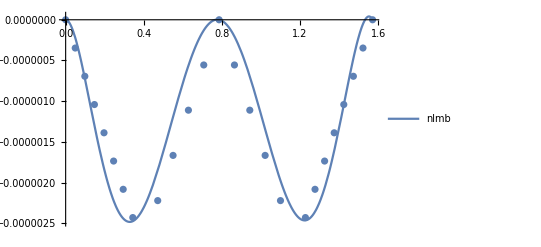

```mathematica
(*Fitting bdata*)
bmodel=ab+bb x^2+cb x^3+db x^4+eb x^5+fb x^6(*+gb x^7+hb x^8*)
(*nlma=NonlinearModelFit[adata,{amodel,(amodel/.x->0)==54,(amodel/.x->Pi/8)==46,(amodel/.x->Pi/4)==41,(amodel/.x->(3*Pi)/8)==46,(amodel/.x->Pi/2)==54},{aa,ba,ca,da},x]//Normal(*,ea,fa,ga,ha*)*)(*USe this one for the 8th order model*)
nlmb=NonlinearModelFit[bdata,{bmodel,(bmodel/.x->0)==0,(bmodel/.x->Pi/4)==0,(bmodel/.x->Pi/2)==0},{ab,bb,cb,db,eb,fb},x]//Normal
Show[Plot[nlmb,{x,0,Pi/2},PlotStyle->Thick,PlotLegends->{"nlmb"}],ListPlot[bdata]]
```

aM+bM x^2+cM x^3+dM x^4+eM x^5+fM x^6

0.01+0.481608 x^2-1.95421 x^3+2.7841 x^4-1.67053 x^5+0.360242 x^6

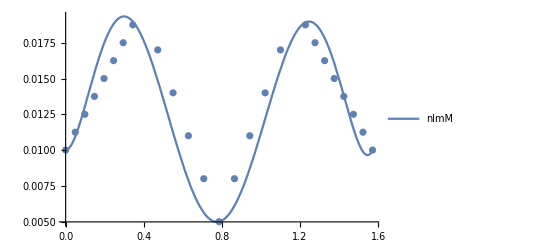

```mathematica
(*Fitting Mdata*)
Mmodel=aM+bM x^2+cM x^3+dM x^4+eM x^5+fM x^6(*+gb x^7+hb x^8*)
(*nlma=NonlinearModelFit[adata,{amodel,(amodel/.x->0)==54,(amodel/.x->Pi/8)==46,(amodel/.x->Pi/4)==41,(amodel/.x->(3*Pi)/8)==46,(amodel/.x->Pi/2)==54},{aa,ba,ca,da},x]//Normal(*,ea,fa,ga,ha*)*)(*USe this one for the 8th order model*)
nlmM=NonlinearModelFit[Mdata,{Mmodel,(Mmodel/.x->0)==0.01,(Mmodel/.x->Pi/4)==0.005,(Mmodel/.x->Pi/2)==0.01},{aM,bM,cM,dM,eM,fM},x]//Normal
Show[Plot[nlmM,{x,0,Pi/2},PlotStyle->Thick,PlotLegends->{"nlmM"}],ListPlot[Mdata]]
```